```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]=4+1/20 (-1-x) (1-x) (3-x) (4-x) (6-x);
xmin=0;xmax=6;
xs=Range[xmin,xmax,(xmax-xmin)/8];
```

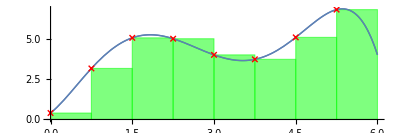

```mathematica
Rectangles=Table[Graphics[{Green,Opacity[0.5],EdgeForm[Thin],Rectangle[{xs[[i]],0},{xs[[i+1]],f[xs[[i]]]}]}]
,{i,Length[xs]-1}];
Marks=ListPlot[Table[{x,f[x]},{x,xs[[1;;Length[xs]-1]]}],PlotStyle->{PointSize[0.5],Red},PlotMarkers-> {"×",Large}];
TrueFunction=Plot[f[x],{x,xmin,xmax},PlotStyle->Thick,AspectRatio->1/3];
Fig=Show[{TrueFunction}~Join~Rectangles~Join~{TrueFunction,Marks}]
Export["left-riemann.pdf",Fig];
```

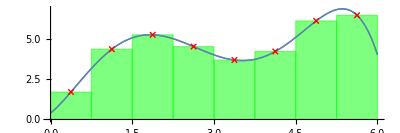

```mathematica
Rectangles=Table[Graphics[{Green,Opacity[0.5],EdgeForm[Thin],Rectangle[{xs[[i]],0},{xs[[i+1]],f[(xs[[i]]+xs[[i+1]])/2]}]}]
,{i,Length[xs]-1}];
Marks=ListPlot[Table[{(xs[[i]]+xs[[i+1]])/2,f[(xs[[i]]+xs[[i+1]])/2]},{i,Length[xs]-1}],PlotStyle->{PointSize[0.5],Red},PlotMarkers-> {"×",Large}];
TrueFunction=Plot[f[x],{x,xmin,xmax},PlotStyle->Thick,AspectRatio->1/3];
Fig=Show[{TrueFunction}~Join~Rectangles~Join~{TrueFunction,Marks}]
Export["midpoint-riemann.pdf",Fig];
```

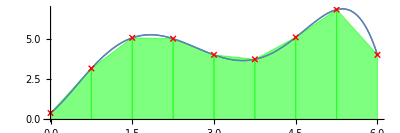

```mathematica
Polygons=Table[Graphics[{Green,Opacity[0.5],EdgeForm[Thin],Polygon[{{xs[[i]],0},{xs[[i]],f[xs[[i]]]} ,{xs[[i+1]],f[xs[[i+1]]]},{xs[[i+1]],0}}]}]
,{i,Length[xs]-1}];
Marks=ListPlot[Table[{x,f[x]},{x,xs}],PlotStyle->{PointSize[0.5],Red},PlotMarkers-> {"×",Large}];
TrueFunction=Plot[f[x],{x,xmin,xmax},PlotStyle->Thick,AspectRatio->1/3];
Fig=Show[{TrueFunction}~Join~Polygons~Join~{TrueFunction,Marks}]
Export["trapezoidal.pdf",Fig];
```

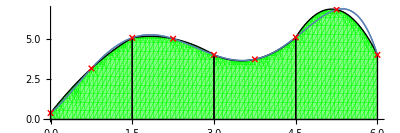

```mathematica
Regions=Table[
data=Table[{xs[[2*i+j]],f[xs[[2*i+j]]]},{j,3}];
parabola = Fit[data, {1,x,x^2}, x];
RegionPlot[xs[[2i+1]]<x<xs[[2i+3]]&&0<y<parabola,{x,xs[[2i+1]],xs[[2i+3]]},{y,0,10},PlotStyle-> {Green,Opacity[0.5]},BoundaryStyle->{Black,Thin}],{i,0,4-1}];
Marks=ListPlot[Table[{x,f[x]},{x,xs}],PlotStyle->{PointSize[0.5],Red},PlotMarkers-> {"×",Large}];
TrueFunction=Plot[f[x],{x,xmin,xmax},PlotStyle->Thick,AspectRatio->1/3,PlotStyle->Red];
Fig=Show[{TrueFunction}~Join~Regions~Join~{TrueFunction,Marks}]
Export["simpson.pdf",Fig];
```